Preliminaries: equations, parameter values, displayParameters function

```mathematica
wDot[w_,hW_,lW_,a_,pW_,kappa_,iIn_,aP_,p_,h_, a2_,h2_,aP2_,p2_]:= 
(pW w)/kappa Log[(hW+iIn)/(hW+iIn Exp[-kappa])]-lW w-a w h-aP w p-a2 w h2 - aP2 w p2 
hDot[eta_,c_,cP_,kappa_,pP_,p_,hP_,iIn_,phi_,a_,w_,h_,aP_,lH_,d_]:=
(1-eta) c/cP (pP p)/(kappa) Log[(hP+iIn)/(hP+iIn Exp[-kappa])] - phi a w h + (1-phi)c a w h+ (1-eta) c aP w p -lH h + d p
pDot[eta_,pP_,p_,kappa_,hP_,iIn_,phi_,a_,w_,h_,aP_,cP_,d_,lP_] :=
eta (pP p)/(kappa) Log[(hP+iIn)/(hP+iIn Exp[-kappa])]+phi a w h +eta aP cP p w - d p - lP p
h2Dot[eta2_,c_,cP_,pP2_,p2_,kappa_,hP2_,iIn_,phi2_,a2_,w_,h2_,aP2_,lH2_,d2_] :=
(1-eta2) c/cP (pP2 p2)/(kappa) Log[(hP2+iIn)/(hP2+iIn Exp[-kappa])]-phi2 a2 w h2 + (1-phi2) c a2 w h2 +(1-eta2) c aP2 w p2 - lH2 h2+d2 p2
p2Dot[eta2_,pP2_,p2_,kappa_,hP2_,iIn_,phi2_,a2_,w_,h2_,aP2_,cP_,d2_,lP2_] :=
eta2 (pP2 p2)/(kappa) Log[(hP2+iIn)/(hP2+iIn Exp[-kappa])]+phi2 a2 w h2+eta2 aP2 cP p2 w-d2 p2-lP2 p2
kappa[kW_, kH_,kP_,kH2_,kP2_,w_,h_,p_,h2_,p2_]:=
kW w+kH h+ kP p+kH2 h2+kP2 p2
```

```mathematica
displayParameters[pW_,pP_,pP2_,kW_,kH_,kP_,kH2_,kP2_,hW_,hP_,hP2_,lW_,lH_,lH2_,lP_,lP2_,a_, a2_,aP_,aP2_,d_,d2_,eta_,phi_, eta2_,phi2_,c_,cP_,iIn_, opts:OptionsPattern[]]:=
{NDSolve[{w'[t]==wDot[w[t],hW,lW,a,pW,kappa[kW,kH,kP,kH2,kP2,w[t],h[t],p[t],0,0],iIn,aP,p[t],h[t],a2,0,aP2,0],h'[t]==hDot[eta,c,cP,kappa[kW,kH,kP,kH2,kP2,w[t],h[t],p[t],0,0],pP,p[t],hP,iIn,phi,a,w[t],h[t],aP,lH,d],p'[t]==pDot[eta,pP,p[t],kappa[kW,kH,kP,kH2,kP2,w[t],h[t],p[t],0,0],hP,iIn,phi,a,w[t],h[t],aP,cP,d,lP],w[0]==1,h[0]==1,p[0]==1},{w,h,p},{t,0,700}, FilterRules[{opts},Options[NDSolve]]],
{{"pW",pW},{"pP",pP},{"pP2", pP2},{"kW",kW},{"kH",kH},{"kP",kP},{"kH2",kH2},{"kP2",kP2},{"hW",hW},{"hP",hP},{"hP2",hP2},{"lW",lW},{"lH",lH},{"lH2",lH2},{"lP",lP},{"lP2",lP2},{"a",a},{"a2",a2},{"aP",aP},{"aP2",aP2},{"d",d},{"d2",d2},{"eta",eta},{"eta2",eta2},{"phi",phi},{"phi2",phi2},{"c", c},{"cP",cP},{"iIn",iIn}}}
opts:OptionsPattern[]
```

opts:OptionsPattern[]

```mathematica
pW=3
pP=2.9
pP2=2.9
kW=0.1
kH=0.05
kP=0.15
kH2=0.015
kP2=0.15
hW=30
hP=30
hP2=30
lW=0.5
lH=0.5
lP=0.1
lH2=0.5
lP2=0.1
d=0.5
d2=0.5
a=0.15
a2=0.15
aP=0
aP2=0
phi=0
phi2=0
c=0.1
cP=0.1
eta=0
eta2=0
iIn=10
```

3

2.9

2.9

0.1

0.05

0.15

0.015

0.15

30

30

30

0.5

0.5

0.1

0.5

0.1

0.5

0.5

0.15

0.15

0

0

0

«1 more identical outputs»

0.1

0.1

0

0

10

```mathematica
displayParameters[pW,pP,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,d,d2,eta,phi, eta2,phi2,c,cP,iIn]
```

{{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}},{{pW,3},{pP,2.9},{pP2,2.9},{kW,0.1},{kH,0.05},{kP,0.15},{kH2,0.015},{kP2,0.15},{hW,30},{hP,30},{hP2,30},{lW,0.5},{lH,0.5},{lH2,0.5},{lP,0.1},{lP2,0.1},{a,0.15},{a2,0.15},{aP,0},{aP2,0},{d,0.8},{d2,0.8},{eta,0},{eta2,0},{phi,1},{phi2,1},{c,0.1},{cP,0.1},{iIn,10}}}

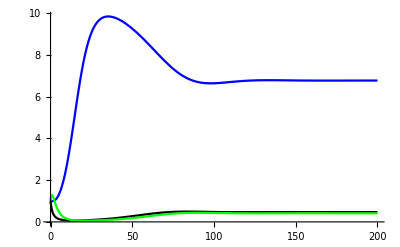

```mathematica
Plot[{w[t]/.%100[[1]],p[t]/.%100[[1]],h[t]/.%100[[1]]},{t,0,200},PlotStyle->{Blue,Black,Green}]
```

```mathematica
displayParameters[pW,pP,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,d,d2,eta,phi, eta2,phi2,c,cP,iIn]
```

{{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}},{{pW,3},{pP,2.9},{pP2,2.9},{kW,0.1},{kH,0.05},{kP,0.15},{kH2,0.015},{kP2,0.15},{hW,30},{hP,30},{hP2,30},{lW,0.5},{lH,0.5},{lH2,0.5},{lP,0.1},{lP2,0.1},{a,0.15},{a2,0.15},{aP,0},{aP2,0},{d,0.8},{d2,0.8},{eta,0},{eta2,0},{phi,1},{phi2,1},{c,0.1},{cP,0.1},{iIn,20}}}

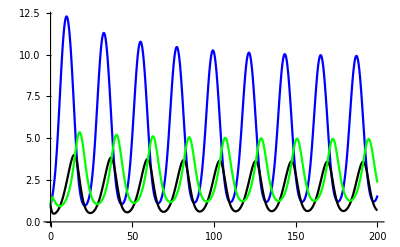

```mathematica
Plot[{w[t]/.%132[[1]],p[t]/.%132[[1]],h[t]/.%132[[1]]},{t,0,200},PlotStyle->{Blue,Black,Green}]
```

```mathematica
displayParameters[pW,pP,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,d,d2,eta,phi, eta2,phi2,c,cP,iIn]
```

{{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}},{{pW,3},{pP,2.9},{pP2,2.9},{kW,0.1},{kH,0.05},{kP,0.15},{kH2,0.015},{kP2,0.15},{hW,30},{hP,30},{hP2,30},{lW,0.5},{lH,0.5},{lH2,0.5},{lP,0.1},{lP2,0.1},{a,0.15},{a2,0.15},{aP,0},{aP2,0},{d,0.8},{d2,0.8},{eta,0},{eta2,0},{phi,1},{phi2,1},{c,0.1},{cP,0.1},{iIn,15}}}

```mathematica
Plot[{w[t]/.%132[[1]],p[t]/.%132[[1]],h[t]/.%132[[1]]},{t,0,200},PlotStyle->{Blue,Black,Green}]
```

-Graphics-

```mathematica
Flatten[Table[{displayParameters[pW,pP,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,eta,phi, eta2,phi2,c,cP,iIn][[1]]},{eta,0,1,0.5},{pP,2.2,2.9,0.1}],3]
```

```mathematica
MatrixPlot[Table[Module[{mean, function=w[t]/.%165[[i,1]]}, 
mean=Integrate[function, {t,500,600}]/(600-500);
{(NIntegrate[Abs[function-mean],{t,500,600}]/(600-500))/mean}],{i,1,24,1}],PlotLegends->Automatic, PlotLabel->"Varying pP and eta"]
```

-Graphics-

So this is with removing the ‘dividing by mean’ part.

```mathematica
MatrixPlot[Table[Module[{mean, function=w[t]/.%165[[i,1]]}, 
mean=Integrate[function, {t,500,600}]/(600-500);
{(NIntegrate[Abs[function-mean],{t,500,600}]/(600-500))}],{i,1,24,1}],PlotLegends->Automatic, PlotLabel->"Varying pP and eta"]
```

-Graphics-

Investigating negatives:

```mathematica
Table[Module[{mean, function=w[t]/.%165[[i,1]]}, 
mean=Integrate[function, {t,500,600}]/(600-500);
{(NIntegrate[Abs[function-mean],{t,500,600}]/(600-500))/mean}],{i,1,24,1}]
```

{{0.00158078},{0.00967105},{0.0449278},{0.144633},{0.302974},{0.437501},{0.54294},{0.628506},{0.657669},{0.745942},{0.863995},{0.924754},{0.936531},{0.924833},{1.03892},{1.16249},{1.46393},{1.17111},{1.27957},{1.04109},{-1.21707},{3.02183},{1.26656},{-0.903692}}

Culprit 1: pP=2.9, eta=1

```mathematica
displayParameters[pW,2.9,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,1,phi, eta2,phi2,c,cP,iIn][[1]]
```

{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

```mathematica
NIntegrate[w[t]/.%177,{t,500,600}]/(600-500)
```

{-4.50542×10^-23}

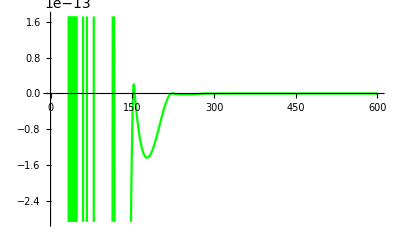

```mathematica
Plot[{w[t]/.%177[[1]]},{t,0,600},PlotStyle->{Blue,Black,Green}]
```

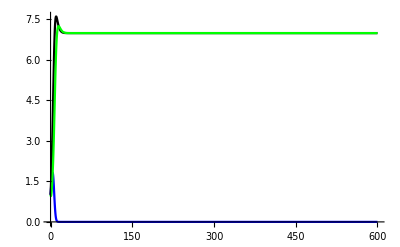

```mathematica
Plot[{w[t]/.%177[[1]], p[t]/.%177[[1]],h[t]/.%177[[1]]},{t,0,600},PlotStyle->{Blue,Black,Green}]
```

```mathematica
displayParameters[pW,2.8,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,1,phi, eta2,phi2,c,cP,iIn][[1]]
```

{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

```mathematica
NIntegrate[w[t]/.%188,{t,500,600}]/(600-500)
```

{2.9295×10^-22}

```mathematica
Flatten[Table[{displayParameters[pW,pP,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,eta,phi, eta2,phi2,c,cP,iIn]},{eta,0,1,0.5},{pP,2.2,2.9,0.1}],3]
```

Culprit 2: pP=2.6, eta=1 (so high eta and high pP causes prey to die)

```mathematica
displayParameters[pW,2.6,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,1,phi, eta2,phi2,c,cP,iIn][[1]]
```

{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

```mathematica
NIntegrate[w[t]/.%191,{t,500,600}]/(600-500)
```

{-4.39031×10^-23}

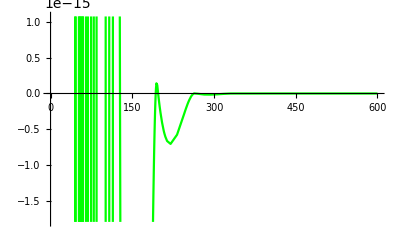

```mathematica
Plot[{w[t]/.%191[[1]]},{t,0,600},PlotStyle->{Blue,Black,Green}]
```

```mathematica
displayParameters[pW,2.5,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,1,phi, eta2,phi2,c,cP,iIn][[1]]
```

{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

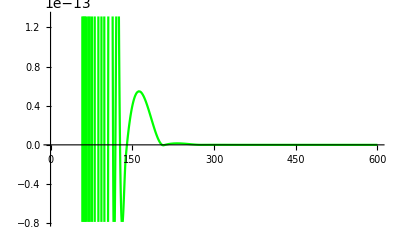

```mathematica
Plot[{w[t]/.%194[[1]]},{t,0,600},PlotStyle->{Blue,Black,Green}]
```

```mathematica
displayParameters[pW,2.2,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,1,phi, eta2,phi2,c,cP,iIn][[1]]
```

{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

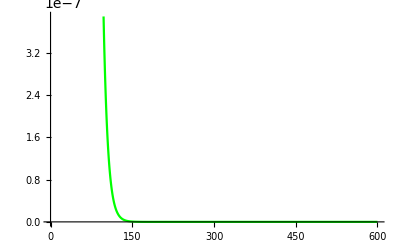

```mathematica
Plot[{w[t]/.%196[[1]]},{t,0,600},PlotStyle->{Blue,Black,Green}]
```

```mathematica
displayParameters[pW,2.4,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,1,phi, eta2,phi2,c,cP,iIn][[1]]
```

{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

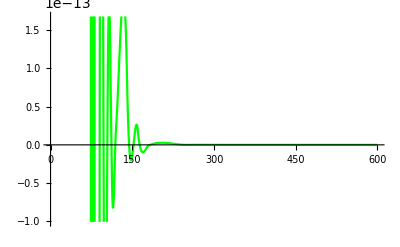

```mathematica
Plot[{w[t]/.%198[[1]]},{t,0,600},PlotStyle->{Blue,Black,Green}]
```

```mathematica
Flatten[Table[{displayParameters[pW,pP,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,eta,phi, eta2,phi2,c,cP,iIn][[1]]},{phi,0,1,0.5},{pP,2.2,2.9,0.1}],3]
```

{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]},{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

```mathematica
MatrixPlot[Table[Module[{mean, function=w[t]/.%211[[i,1]]}, 
mean=Integrate[function, {t,500,600}]/(600-500);
{(NIntegrate[Abs[function-mean],{t,500,600}]/(600-500))}],{i,1,24,1}],PlotLegends->Automatic, PlotLabel->"Varying pP and phi"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {520.87}. NIntegrate obtained 7.67374×10^-13 and 2.33807×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {515.426}. NIntegrate obtained 7.19047×10^-13 and 1.57378×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {523.697}. NIntegrate obtained 3.52517×10^-13 and 7.90611×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

```mathematica
Table[Module[{mean, function=w[t]/.%211[[i,1]]}, 
mean=Integrate[function, {t,500,600}]/(600-500);
{(NIntegrate[Abs[function-mean],{t,500,600}]/(600-500))}],{i,1,24,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {520.87}. NIntegrate obtained 7.67374×10^-13 and 2.33807×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {515.426}. NIntegrate obtained 7.19047×10^-13 and 1.57378×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {523.697}. NIntegrate obtained 3.52517×10^-13 and 7.90611×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{7.67374×10^-15},{7.19047×10^-15},{3.52517×10^-15},{3.92398×10^-16},{3.68719×10^-15},{5.09461×10^-15},{1.78916×10^-15},{9.66356×10^-12},{1.58863×10^-10},{2.87932×10^-11},{3.16451×10^-11},{4.92477×10^-9},{3.64462×10^-9},{8.25944×10^-9},{9.92984×10^-8},{2.99578×10^-7},{0.00693052},{0.0396032},{0.172712},{0.523402},{1.11672},{1.67868},{2.11467},{2.40064}}

Table of mean values

```mathematica
Table[Module[{mean, function=w[t]/.%211[[i,1]]}, 
mean=Integrate[function, {t,500,600}]/(600-500);
{mean}],{i,1,24,1}]
```

{{20.633},{20.633},{20.633},{20.633},{20.633},{20.633},{20.633},{20.633},{8.73076},{8.1571},{7.65518},{7.21217},{6.81817},{6.46538},{6.14761},{5.85986},{4.38424},{4.09503},{3.84422},{3.61883},{3.68587},{3.83696},{3.89485},{3.81959}}

```mathematica
Flatten[Table[{displayParameters[pW,pP,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,eta,phi, eta2,phi2,c,cP,iIn]},{phi,0,1,0.5},{pP,2.2,2.9,0.1}],3]
```

Trying to figure out weird integration stuff. Calculating means is fine.

```mathematica
Integrate[w[t]/.%211[[1,1]],{t,500,600}]/(600-500)
```

20.633

```mathematica
NIntegrate[Abs[w[t]/.%211[[1,1]]-%235[[1]]],{t,500,600}]
```

ReplaceAll::reps: {-20.633+(w→«1»)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Abs[w[t]/.{-20.633+(w→InterpolatingFunction[{{«2»}},{5,7,1,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«154»}},{Developer`PackedArrayForm,{«155»},{«308»}},{Automatic}])}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{500,600}}.

NIntegrate[Abs[w[t]/.%211⟦1,1⟧-%235⟦1⟧],{t,500,600}]

```mathematica
Table[Module[{mean, function=w[t]/.%211[[i,1]]}, 
mean=Integrate[function, {t,500,600}]/(600-500);
{(NIntegrate[Abs[function-mean],{t,500,600}]/(600-500))}],{i,11,24,1}]
```

{{3.16451×10^-11},{4.92477×10^-9},{3.64462×10^-9},{8.25944×10^-9},{9.92984×10^-8},{2.99578×10^-7},{0.00693052},{0.0396032},{0.172712},{0.523402},{1.11672},{1.67868},{2.11467},{2.40064}}

```mathematica
Module[{mean, function=w[t]/.%211[[2,1]]}, 
mean=Integrate[function, {t,500,600}]/(600-500);
{NIntegrate[Abs[function-mean],{t,500,600}]/(600-500)}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {515.426}. NIntegrate obtained 7.19047×10^-13 and 1.57378×10^-16 for the integral and error estimates.

{7.19047×10^-15}

```mathematica
Abs[(w[t]/.%211[[1,1]])-%212]
```

Abs[-20.633+InterpolatingFunction[…][t]]

```mathematica
Integrate[w[t]/.%211[[2,1]],{t,500,600}]/(600-500)
```

20.633

```mathematica
Integrate[w[t]/.%211[[7,1]],{t,500,600}]/(600-500)
```

20.633

```mathematica
Integrate[w[t]/.%211[[10,1]],{t,500,600}]/(600-500)
```

8.1571

Seems like function is constant at a value (but subtly oscillating around it)

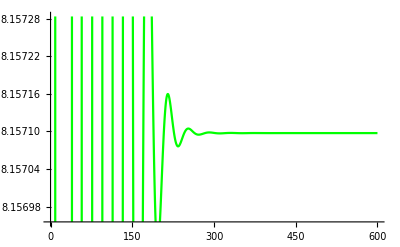

```mathematica
Plot[w[t]/.%211[[10,1]],{t,0,600},PlotStyle->{Blue,Black,Green}]
```

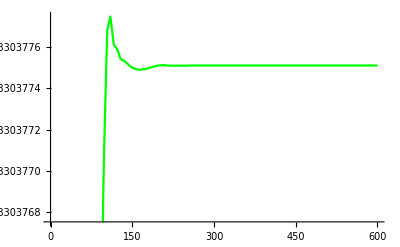

```mathematica
Plot[w[t]/.%211[[1,1]],{t,0,600},PlotStyle->{Blue,Black,Green}]
```

Trying to understand the weird numerical errors we’re getting

```mathematica
displayParameters[pW,2.2,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,eta,0, eta2,phi2,c,cP,iIn][[1]]
```

{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

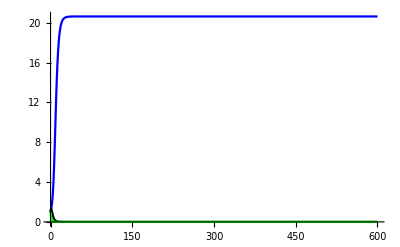

```mathematica
Plot[{w[t]/.%220[[1]], h[t]/.%220[[1]],p[t]/.%220[[1]]},{t,0,600},PlotStyle->{Blue,Black,Green}]
```

```mathematica
displayParameters[pW,2.3,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,eta,0, eta2,phi2,c,cP,iIn][[1]]
```

{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

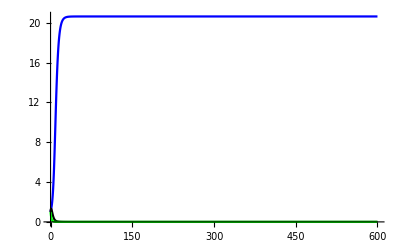

```mathematica
Plot[{w[t]/.%226, h[t]/.%226,p[t]/.%226},{t,0,600},PlotStyle->{Blue,Black,Green}]
```

```mathematica
displayParameters[pW,2.9,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,lH,lH2,lP,lP2,a, a2,aP,aP2,0.5,d2,eta,1, eta2,phi2,c,cP,iIn][[1]]
```

{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

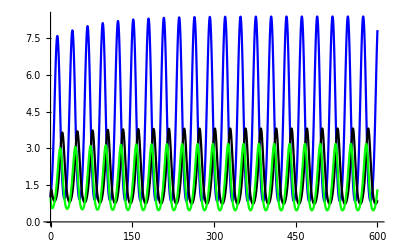

```mathematica
Plot[{w[t]/.%276, h[t]/.%276,p[t]/.%276},{t,0,600},PlotStyle->{Blue,Black,Green}]
```

1. Simulate to equilibrium

```mathematica
displayParameters[pW,pP,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,0.05,lH2,lP,lP2,a, a2,aP,aP2,d,d2,eta,phi, eta2,phi2,c,cP,10]
```

{{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}},{{pW,3},{pP,2.9},{pP2,2.9},{kW,0.1},{kH,0.05},{kP,0.15},{kH2,0.015},{kP2,0.15},{hW,30},{hP,30},{hP2,30},{lW,0.5},{lH,0.05},{lH2,0.5},{lP,0.1},{lP2,0.1},{a,0.15},{a2,0.15},{aP,0},{aP2,0},{d,0.5},{d2,0.5},{eta,0},{eta2,0},{phi,0},{phi2,0},{c,0.1},{cP,0.1},{iIn,10}}}

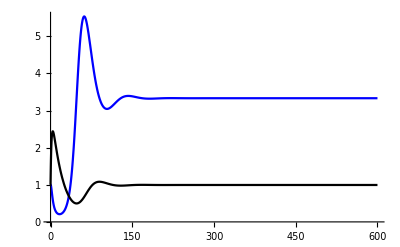

```mathematica
Plot[{w[t]/.%437[[1]], h[t]/.%437[[1]]},{t,0,600},PlotStyle->{Blue,Black,Green}]
```

Equilibrium population sizes (lH=0.05)

```mathematica
w[500]/.%437[[1]]
```

{3.33333}

```mathematica
h[500]/.%437[[1]]
```

{0.994947}

```mathematica
p[500]/.%437[[1]]
```

{-3.4916×10^-12}

```mathematica
displayParameters[pW,pP,pP2,kW,kH,kP,kH2,kP2,hW,hP,hP2,lW,0.1,lH2,lP,lP2,a, a2,aP,aP2,d,d2,eta,phi, eta2,phi2,c,cP,iIn]
```

{{{w→InterpolatingFunction[…],h→InterpolatingFunction[…],p→InterpolatingFunction[…]}},{{pW,3},{pP,2.9},{pP2,2.9},{kW,0.1},{kH,0.05},{kP,0.15},{kH2,0.015},{kP2,0.15},{hW,30},{hP,30},{hP2,30},{lW,0.5},{lH,0.1},{lH2,0.5},{lP,0.1},{lP2,0.1},{a,0.15},{a2,0.15},{aP,0},{aP2,0},{d,0.5},{d2,0.5},{eta,0},{eta2,0},{phi,0},{phi2,0},{c,0.1},{cP,0.1},{iIn,10}}}

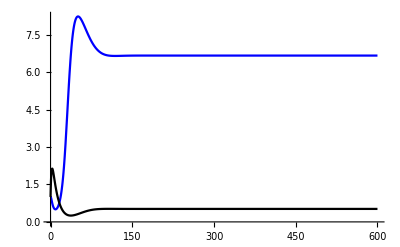

```mathematica
Plot[{w[t]/.%444[[1]], h[t]/.%444[[1]]},{t,0,600},PlotStyle->{Blue,Black,Green}]
```

Equilibrium pop sizes (lH=0.1)

```mathematica
w[500]/.%444[[1]]
```

{6.66667}

```mathematica
h[500]/.%437[[1]]
```

{0.994947}